```mathematica
Table[Expand[ a(x)(x-1)+b x],{a,3},{b,3}]//Flatten//DeleteDuplicates
```

{x^2,x+x^2,2 x+x^2,-x+2 x^2,2 x^2,x+2 x^2,-2 x+3 x^2,-x+3 x^2,3 x^2}

```mathematica
Select[Table[Expand[ a(x)(x-1)+b x],{a,1,6},{b,-3,0}]//Flatten//DeleteDuplicates,Last[CoefficientList[#,x]]==1&]
```

{-4 x+x^2,-3 x+x^2,-2 x+x^2,-x+x^2}

```mathematica
CoefficientList[-x+3 x^2,x]
```

{0,-1,3}

```mathematica
Map[CompleteBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[allGraphs3[k,"graph"],x],{k,Keys[allGraphs3]}]]]//TableForm
```

0 | 1 | 3 | 1
0 | 0 | 2 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 1
0 | 0 | 1 | 
0 | 1 | 1 | 
0 | 1 |  |

```mathematica
With[{keys=allGraphs2},
Sort[Map[CompleteBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[keys[k,"graph"],x],{k,Keys[keys]}]]]]//TableForm
]
```

0 | 1 | 
0 | 0 | 1
0 | 1 | 1

```mathematica
With[{keys=allGraphs3},
Sort[Map[CompleteBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[keys[k,"graph"],x],{k,Keys[keys]}]]]]//TableForm
]
```

0 | 1 |  | 
0 | 0 | 1 | 
0 | 1 | 1 | 
0 | 0 | 0 | 1
0 | 0 | 1 | 1
0 | 0 | 2 | 1
0 | 1 | 3 | 1

```mathematica
With[{keys=allGraphs4},
Sort[Map[CompleteBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[keys[k,"graph"],x],{k,Keys[keys]}]]]]//TableForm
]
```

0 | 1 |  |  | 
0 | 0 | 1 |  | 
0 | 1 | 1 |  | 
0 | 0 | 0 | 1 | 
0 | 0 | 1 | 1 | 
0 | 0 | 2 | 1 | 
0 | 1 | 3 | 1 | 
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 2 | 1
0 | 0 | 0 | 3 | 1
0 | 0 | 1 | 2 | 1
0 | 0 | 1 | 3 | 1
0 | 0 | 2 | 4 | 1
0 | 0 | 4 | 5 | 1
0 | 1 | 7 | 6 | 1

```mathematica
With[{keys=allGraphs5},
Sort[Map[CompleteBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[keys[k,"graph"],x],{k,Keys[keys]}]]]]//TableForm
]
```

0 | 1 |  |  |  | 
0 | 0 | 1 |  |  | 
0 | 1 | 1 |  |  | 
0 | 0 | 0 | 1 |  | 
0 | 0 | 1 | 1 |  | 
0 | 0 | 2 | 1 |  | 
0 | 1 | 3 | 1 |  | 
0 | 0 | 0 | 0 | 1 | 
0 | 0 | 0 | 1 | 1 | 
0 | 0 | 0 | 2 | 1 | 
0 | 0 | 0 | 3 | 1 | 
0 | 0 | 1 | 2 | 1 | 
0 | 0 | 1 | 3 | 1 | 
0 | 0 | 2 | 4 | 1 | 
0 | 0 | 4 | 5 | 1 | 
0 | 1 | 7 | 6 | 1 | 
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 2 | 1
0 | 0 | 0 | 0 | 3 | 1
0 | 0 | 0 | 0 | 4 | 1
0 | 0 | 0 | 1 | 2 | 1
0 | 0 | 0 | 1 | 3 | 1
0 | 0 | 0 | 2 | 3 | 1
0 | 0 | 0 | 2 | 4 | 1
0 | 0 | 0 | 3 | 4 | 1
0 | 0 | 0 | 3 | 5 | 1
0 | 0 | 0 | 4 | 5 | 1
0 | 0 | 0 | 5 | 5 | 1
0 | 0 | 0 | 6 | 6 | 1
0 | 0 | 0 | 9 | 7 | 1
0 | 0 | 1 | 4 | 4 | 1
0 | 0 | 1 | 5 | 5 | 1
0 | 0 | 1 | 7 | 6 | 1
0 | 0 | 2 | 7 | 6 | 1
0 | 0 | 2 | 10 | 7 | 1
0 | 0 | 4 | 14 | 8 | 1
0 | 0 | 8 | 19 | 9 | 1
0 | 1 | 15 | 25 | 10 | 1

```mathematica
Table[falling[x,k],{k,0,6}]
```

{1,x,(-1+x) x,(-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,(-4+x) (-3+x) (-2+x) (-1+x) x,(-5+x) (-4+x) (-3+x) (-2+x) (-1+x) x}

```mathematica
Block[{previous={},current,current2,prev2},
Table[n->(With[{keys=allGraphs6},
current=DeleteDuplicates[Sort[DeleteDuplicates[Table[ChromaticPolynomial[keys[k,"graph"],x],{k,Select[Keys[keys],VertexCount[keys[#,"graph"]]==n&]}]]]];
prev2=Map[Expand[#*x]&,previous];
current2=Table[If[MemberQ[prev2,row],Map[Style[#,Bold]&,row],row],{row,current}];
previous=current;
TableForm[current2]]),{n,1,6}]]
```

{1→x,2→x^2
-x+x^2,3→x^3
2 x-3 x^2+x^3
x-2 x^2+x^3
-x^2+x^3,4→x^4
-6 x+11 x^2-6 x^3+x^4
-4 x+8 x^2-5 x^3+x^4
-2 x+5 x^2-4 x^3+x^4
-3 x+6 x^2-4 x^3+x^4
2 x^2+-3 x^3+x^4
-x+3 x^2-3 x^3+x^4
x^2+-2 x^3+x^4
-x^3+x^4,5→x^5
24 x-50 x^2+35 x^3-10 x^4+x^5
18 x-39 x^2+29 x^3-9 x^4+x^5
12 x-28 x^2+23 x^3-8 x^4+x^5
14 x-31 x^2+24 x^3-8 x^4+x^5
6 x-17 x^2+17 x^3-7 x^4+x^5
8 x-20 x^2+18 x^3-7 x^4+x^5
10 x-23 x^2+19 x^3-7 x^4+x^5
-6 x^2+11 x^3+-6 x^4+x^5
4 x-12 x^2+13 x^3-6 x^4+x^5
6 x-15 x^2+14 x^3-6 x^4+x^5
7 x-17 x^2+15 x^3-6 x^4+x^5
-4 x^2+8 x^3+-5 x^4+x^5
2 x-7 x^2+9 x^3-5 x^4+x^5
4 x-10 x^2+10 x^3-5 x^4+x^5
3 x-9 x^2+10 x^3-5 x^4+x^5
-2 x^2+5 x^3+-4 x^4+x^5
x-4 x^2+6 x^3-4 x^4+x^5
-3 x^2+6 x^3+-4 x^4+x^5
2 x^3+-3 x^4+x^5
-x^2+3 x^3+-3 x^4+x^5
x^3+-2 x^4+x^5
-x^4+x^5,6→x^6
-120 x+274 x^2-225 x^3+85 x^4-15 x^5+x^6
-96 x+224 x^2-190 x^3+75 x^4-14 x^5+x^6
-72 x+174 x^2-155 x^3+65 x^4-13 x^5+x^6
-78 x+185 x^2-161 x^3+66 x^4-13 x^5+x^6
-48 x+124 x^2-120 x^3+55 x^4-12 x^5+x^6
-54 x+135 x^2-126 x^3+56 x^4-12 x^5+x^6
-60 x+146 x^2-132 x^3+57 x^4-12 x^5+x^6
-64 x+154 x^2-137 x^3+58 x^4-12 x^5+x^6
-24 x+74 x^2-85 x^3+45 x^4-11 x^5+x^6
-36 x+96 x^2-97 x^3+47 x^4-11 x^5+x^6
-42 x+107 x^2-103 x^3+48 x^4-11 x^5+x^6
-48 x+118 x^2-109 x^3+49 x^4-11 x^5+x^6
-46 x+115 x^2-108 x^3+49 x^4-11 x^5+x^6
24 x^2+-50 x^3+35 x^4+-10 x^5+x^6
-18 x+57 x^2-68 x^3+38 x^4-10 x^5+x^6
-24 x+68 x^2-74 x^3+39 x^4-10 x^5+x^6
-30 x+79 x^2-80 x^3+40 x^4-10 x^5+x^6
-28 x+76 x^2-79 x^3+40 x^4-10 x^5+x^6
-34 x+87 x^2-85 x^3+41 x^4-10 x^5+x^6
-32 x+84 x^2-84 x^3+41 x^4-10 x^5+x^6
-38 x+95 x^2-90 x^3+42 x^4-10 x^5+x^6
18 x^2+-39 x^3+29 x^4+-9 x^5+x^6
-12 x+40 x^2-51 x^3+31 x^4-9 x^5+x^6
-18 x+51 x^2-57 x^3+32 x^4-9 x^5+x^6
-16 x+48 x^2-56 x^3+32 x^4-9 x^5+x^6
-14 x+45 x^2-55 x^3+32 x^4-9 x^5+x^6
-22 x+59 x^2-62 x^3+33 x^4-9 x^5+x^6
-20 x+56 x^2-61 x^3+33 x^4-9 x^5+x^6
-26 x+67 x^2-67 x^3+34 x^4-9 x^5+x^6
-24 x+64 x^2-66 x^3+34 x^4-9 x^5+x^6
-22 x+61 x^2-65 x^3+34 x^4-9 x^5+x^6
-31 x+78 x^2-75 x^3+36 x^4-9 x^5+x^6
12 x^2+-28 x^3+23 x^4+-8 x^5+x^6
-6 x+23 x^2-34 x^3+24 x^4-8 x^5+x^6
14 x^2+-31 x^3+24 x^4+-8 x^5+x^6
-8 x+28 x^2-38 x^3+25 x^4-8 x^5+x^6
-14 x+39 x^2-44 x^3+26 x^4-8 x^5+x^6
-12 x+36 x^2-43 x^3+26 x^4-8 x^5+x^6
-10 x+33 x^2-42 x^3+26 x^4-8 x^5+x^6
-16 x+44 x^2-48 x^3+27 x^4-8 x^5+x^6
-14 x+41 x^2-47 x^3+27 x^4-8 x^5+x^6
-17 x+47 x^2-51 x^3+28 x^4-8 x^5+x^6
-15 x+44 x^2-50 x^3+28 x^4-8 x^5+x^6
6 x^2+-17 x^3+17 x^4+-7 x^5+x^6
8 x^2+-20 x^3+18 x^4+-7 x^5+x^6
-4 x+16 x^2-25 x^3+19 x^4-7 x^5+x^6
10 x^2+-23 x^3+19 x^4+-7 x^5+x^6
-8 x+24 x^2-30 x^3+20 x^4-7 x^5+x^6
-6 x+21 x^2-29 x^3+20 x^4-7 x^5+x^6
-10 x+29 x^2-34 x^3+21 x^4-7 x^5+x^6
-9 x+27 x^2-33 x^3+21 x^4-7 x^5+x^6
-7 x+24 x^2-32 x^3+21 x^4-7 x^5+x^6
-6 x^3+11 x^4+-6 x^5+x^6
4 x^2+-12 x^3+13 x^4+-6 x^5+x^6
-2 x+9 x^2-16 x^3+14 x^4-6 x^5+x^6
6 x^2+-15 x^3+14 x^4+-6 x^5+x^6
-4 x+14 x^2-20 x^3+15 x^4-6 x^5+x^6
-5 x+15 x^2-20 x^3+15 x^4-6 x^5+x^6
-3 x+12 x^2-19 x^3+15 x^4-6 x^5+x^6
7 x^2+-17 x^3+15 x^4+-6 x^5+x^6
-4 x^3+8 x^4+-5 x^5+x^6
2 x^2+-7 x^3+9 x^4+-5 x^5+x^6
4 x^2+-10 x^3+10 x^4+-5 x^5+x^6
-x+5 x^2-10 x^3+10 x^4-5 x^5+x^6
3 x^2+-9 x^3+10 x^4+-5 x^5+x^6
-2 x^3+5 x^4+-4 x^5+x^6
x^2+-4 x^3+6 x^4+-4 x^5+x^6
-3 x^3+6 x^4+-4 x^5+x^6
2 x^4+-3 x^5+x^6
-x^3+3 x^4+-3 x^5+x^6
x^4+-2 x^5+x^6
-x^5+x^6}

```mathematica
Table[n->(With[{keys=allGraphs6},
Sort[Map[NullBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[keys[k,"graph"],x],{k,Select[Keys[keys],VertexCount[keys[#,"graph"]]==n&]}]]]]//DeleteDuplicates//Length]),{n,1,6}]
```

{1→1,2→2,3→4,4→9,5→23,6→73}

```mathematica
With[{keys=allGraphs6},
Sort[Map[CompleteBaseCoeff,DeleteDuplicates[Table[ChromaticPolynomial[keys[k,"graph"],x],{k,Keys[keys]}]]]]//TableForm
]
```

Keys::invrl: The argument $Failed is not a valid Association or a list of rules.

Table::iterb: Iterator {k,Keys[$Failed]} does not have appropriate bounds.

Table::nliter: Non-list iterator CompleteBaseCoeff[{k,Keys[$Failed]}] at position 2 does not evaluate to a real numeric value.

Table[CompleteBaseCoeff[ChromaticPolynomial[$Failed[k,graph],x]],CompleteBaseCoeff[{k,Keys[$Failed]}]]

```mathematica
DeleteDuplicates[Table[ChromaticPolynomial[allGraphs2[k,"graph"],x],{k,Keys[allGraphs2]}]]
```

{x^2,-x+x^2,x}

```mathematica
Table[allGraphs2[k,"graph"]->ChromaticPolynomial[allGraphs2[k,"graph"],x],{k,Keys[allGraphs2]}]
```

{-Graphics-→x^2,-Graphics-→-x+x^2,-Graphics-→x}

```mathematica
CompleteBaseCoeff2[5 x-6 x^2+x^3]
```

{0,0,-3,1}

```mathematica
CompletePoly2[l_List]:=Table[l[[k]]*CompletePoly2[Length[l]-1,k],{k,Length[l]}]
```

```mathematica
CompletePoly2[{0,0,-3,1}]//Total//Expand
```

-4 x+6 x^2-2 x^3

```mathematica
With[{n=2},Product[x-i,{i,0,n-1}]]
```

(-1+x) x

```mathematica
CompletePoly[2,1]//Factor
```

CompletePoly[2,1]

```mathematica
MatrixForm[Table[Expand[ a(x)(x-1)(x-2)+b x(x-1)],{a,1,6},{b,-3,0}],TableHeadings->{Range[6],Range[-3,0]}]
```

( | -3 | -2 | -1 | 0
1 | 5 x-6 x^2+x^3 | 4 x-5 x^2+x^3 | 3 x-4 x^2+x^3 | 2 x-3 x^2+x^3
2 | 7 x-9 x^2+2 x^3 | 6 x-8 x^2+2 x^3 | 5 x-7 x^2+2 x^3 | 4 x-6 x^2+2 x^3
3 | 9 x-12 x^2+3 x^3 | 8 x-11 x^2+3 x^3 | 7 x-10 x^2+3 x^3 | 6 x-9 x^2+3 x^3
4 | 11 x-15 x^2+4 x^3 | 10 x-14 x^2+4 x^3 | 9 x-13 x^2+4 x^3 | 8 x-12 x^2+4 x^3
5 | 13 x-18 x^2+5 x^3 | 12 x-17 x^2+5 x^3 | 11 x-16 x^2+5 x^3 | 10 x-15 x^2+5 x^3
6 | 15 x-21 x^2+6 x^3 | 14 x-20 x^2+6 x^3 | 13 x-19 x^2+6 x^3 | 12 x-18 x^2+6 x^3)

```mathematica
Select[Table[Expand[ a(x)(x-1)(x-2)+b x(x-1)],{a,1,6},{b,-3,0}]//Flatten//DeleteDuplicates,Last[CoefficientList[#,x]]==1&]
```

```mathematica
{5 x-6 x^2+x^3,4 x-5 x^2+x^3,3 x-4 x^2+x^3,2 x-3 x^2+x^3}
```

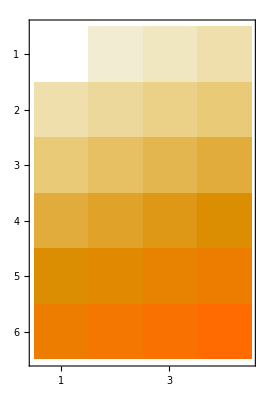

```mathematica
MatrixPlot[Table[Factor[ a(x)(x-1)+b x]/.x->4,{a,1,6},{b,-3,0}]]
```